## Setup Distributions

Define 3 potentials to find the equilibrium measure

```mathematica
VA[x_]:=x^2;
VB[x_]:=x^4;
VC[x_]:=Exp[x]-x;
```

Compute the support of the equilibrium measure and contruct a Chebyshev approximation of the potential. 

 Fun[f,Line[{a,b}] constructs a Chebyshev approximation of f on the interval [a,b].
 
 SingFun[fun,{0,0}] represents a fun with 0 singularities at its endpoint

```mathematica
vfA=SingFun[Fun[VA',VA//EquilibriumMeasureSupport//Line],{0,0}];
vfB=SingFun[Fun[VB',VB//EquilibriumMeasureSupport//Line],{0,0}];
vfC=SingFun[Fun[VC',VC//EquilibriumMeasureSupport//Line],{0,0}];
```

Convert from potential to equilibrium measure.  The representation is now

 SingFun[fun,{1/2,1/2}] 
 
 where fun is a smooth Chebyshev approximation, and the 1/2s denote square root singularities at the endpoints.

```mathematica
emA=(-1/(2 π) vfA//HilbertInverse);
emB=(-1/(2 π) vfB//HilbertInverse);
emC=(-1/(2 π) vfC//HilbertInverse);
G=LFun[Exp[-#^2]/Sqrt[π]&,RealLine,80];
MP=MarchenkoPastur[1.,.1];
```

We plot the measures

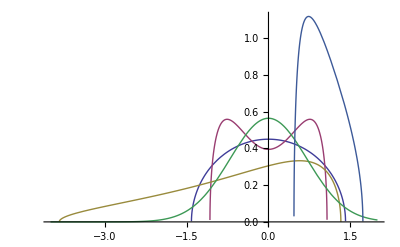

```mathematica
Plot[{emA[x],emB[x],emC[x],G[x]//Re,MP[x]},{x,-4,2}]
```

### Histograms

emA is the semicircle distribution

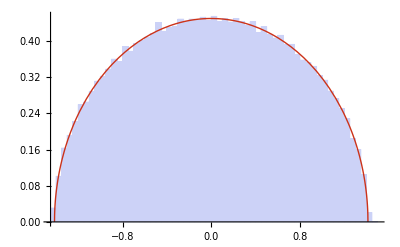

```mathematica
HistogramPlot[RandomSymmetric[300],emA]
```

G is the Gaussian distribution

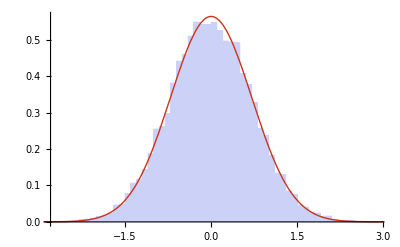

```mathematica
n=150;
HistogramPlot[(Q=RandomOrthogonal[n];Λ=DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]];
Q.Λ.Transpose[Q]),G]
```

MP is the Marchenko–Pastur distribution

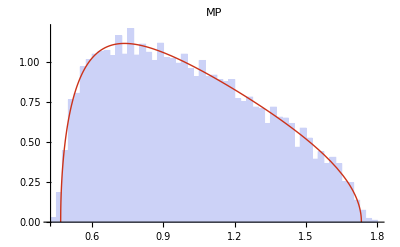

```mathematica
m=70;n=10 m;
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
A.Transpose[A]),MP,PlotLabel->"MP"]
```

## Square Root FreePlus Examples

Free probability add A with itself.  Returns another function of the form  SingFun[fun,{1/2,1/2}]

```mathematica
AA=emA~FreePlus~emA;
```

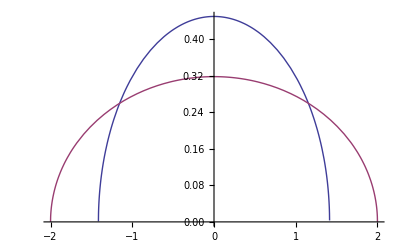

```mathematica
Plot[{emA[x],AA[x]},{x,-2,2}]
```

We can check the RTransforms agree

```mathematica
RTransform[AA,.1 I]-2RTransform[emA,.1 I]
```

-1.11022×10^-16+1.42109×10^-14 ⅈ

We can compare against the histogram:

Free probability add A and B (don’t worry about the warnings)

```mathematica
AB=emA~FreePlus~emB;
```

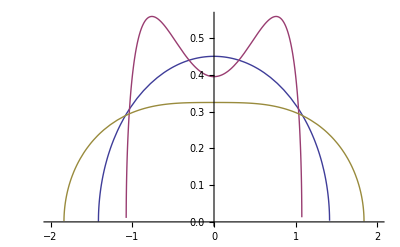

```mathematica
Plot[{emA[x],emB[x],AB[x]},{x,-2,2}]
```

We can check the RTransforms agree

```mathematica
RTransform[AB,.1 I]-(RTransform[emA,.1 I]+RTransform[emB,.1 I])
```

4.08421×10^-14+1.22569×10^-13 ⅈ

Free probability add A and C

```mathematica
AC=emA~FreePlus~emC;
```

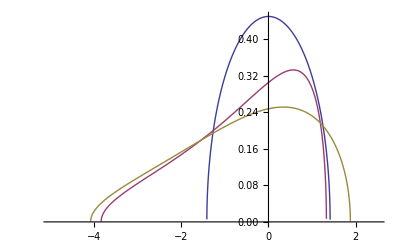

```mathematica
Plot[{emA[x],emC[x],AC[x]},{x,-5,2.5}]
```

We can check the RTransforms agree

```mathematica
RTransform[AC,.1 I]-(RTransform[emA,.1 I]+RTransform[emC,.1 I])
```

1.27232×10^-13-2.06057×10^-13 ⅈ

We can add the semi circle to Marchenko–Pastur distribution

```mathematica
AMP=emA~FreePlus~MP;
```

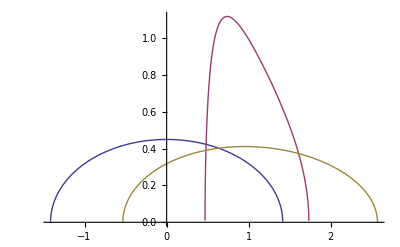

```mathematica
Plot[{emA[x],MP[x],AMP[x]},{x,-2.,3.},PlotRange->All]
```

### Histograms

We verify the semicircle ⊕ semicircle

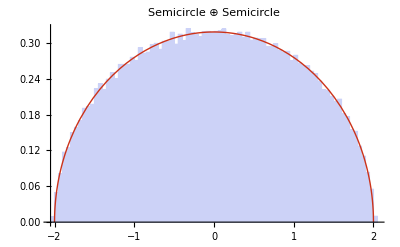

```mathematica
n=300;
HistogramPlot[(
A=RandomSymmetric[n];
B=RandomSymmetric[n];
A+B),AA,PlotLabel->"Semicircle ⊕ Semicircle"]
```

Here we verify the free addition of a  Marchenko–Pastur distribution with a semicircle

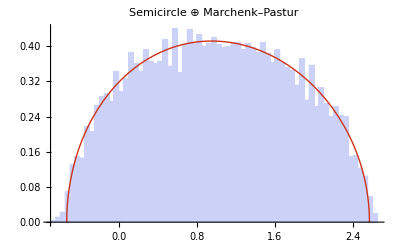

```mathematica
m=70;n=10 m;
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
B=RandomSymmetric[m];
A.Transpose[A]+B),AMP,PlotLabel->"Semicircle ⊕ Marchenk–Pastur"]
```

## Gaussian FreePlus Examples

Gaussian examples (limited sample points means the accuracy won’t be quite as high here).  FreeAddRealLine means we assume the added measure is supported on the real line

```mathematica
GG=G~FreePlus~G;
```

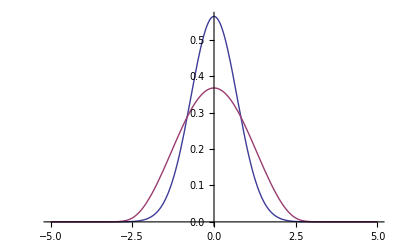

```mathematica
Plot[{G[x]//Re,GG[x]//Re}//Evaluate,{x,-5,5.}]
```

```mathematica
RTransform[GG,.1 I]-(RTransform[G,.1 I]+RTransform[G,.1 I])
```

0.000579164+0.000451391 ⅈ

```mathematica
AG=emA~FreePlus~G;
```

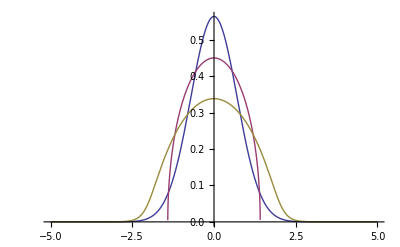

```mathematica
Plot[{G[x]//Re,emA[x],AG[x]//Re},{x,-5,5.}]
```

```mathematica
BG=emB~FreePlus~G;
```

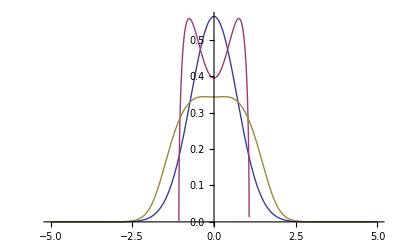

```mathematica
Plot[{G[x]//Re,emB[x],BG[x]//Re},{x,-5,5.}]
```

```mathematica
MPG=MP~FreePlus~G;
```

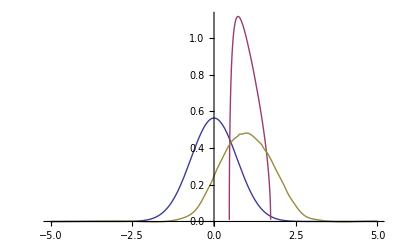

```mathematica
Plot[{G[x]//Re,MP[x],MPG[x]//Re},{x,-5,5.}]
```

### Histograms

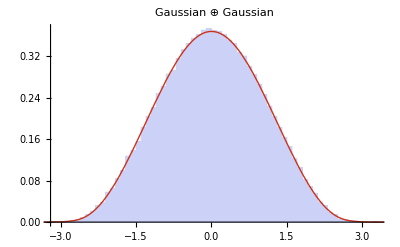

```mathematica
n=300;
HistogramPlot[(
Q=RandomOrthogonal[n];
A=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
Q=RandomOrthogonal[n];
B=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
A+B),GG,PlotLabel->"Gaussian ⊕ Gaussian"]
```

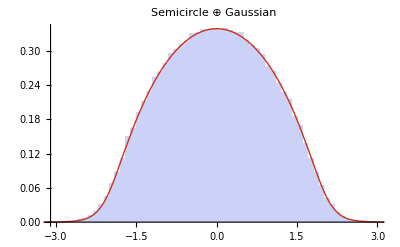

```mathematica
n=300;
HistogramPlot[(
A=RandomSymmetric[n];
Q=RandomOrthogonal[n];
B=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
A+B),AG,PlotLabel->"Semicircle ⊕ Gaussian"]
```

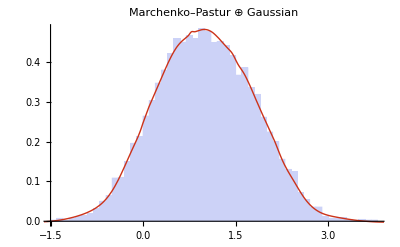

```mathematica
m=70;n=10 m;
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
Q=RandomOrthogonal[m];
B=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],m]].Transpose[Q];
A.Transpose[A]+B),MPG,PlotLabel->"Marchenko–Pastur ⊕ Gaussian"]
```

## Finite n FreePlus Examples

We construct a counting measure which approximates the semicircle

```mathematica
n=50;An=PFun[{1/n},Point[#]]&/@((A=RandomSymmetric[n])//Eigenvalues);
```

There Stieljes transforms are close:

```mathematica
Stieljes[An,1. I]-Stieljes[emA,1.I]
```

-0.00106955-0.0107681 ⅈ

We construct an approximation of the Stieljes function on an ellipse:

```mathematica
EAn=LFun[1/(-2π I)Stieljes[An,#]&,Ellipse[{-Sqrt[2],Sqrt[2]},.8 ],150];
```

It’s Stieljestransform is identical to An:

```mathematica
Stieljes[An,1. I]-Stieljes[EAn,1. I]
```

1.16443×10^-16-1.11022×10^-16 ⅈ

We compute the FreePlus (can take a while)

```mathematica
AAn=emA~FreePlus~EAn;
```

It matches the true measure very closely:

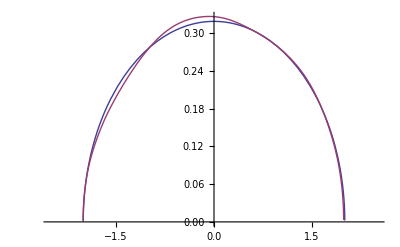

```mathematica
Plot[{AA[x],AAn[x]},{x,-2.5,2.5}]
```

We repeat the experiment with large n

```mathematica
n=500;An=PFun[{1/n},Point[#]]&/@(RandomSymmetric[n]//Eigenvalues);
EAn=LFun[1/(-2π I)Stieljes[An,#]&,Ellipse[{-Sqrt[2],Sqrt[2]},.8 ],150];
```

```mathematica
AAn=emA~FreePlus~EAn;
```

Now they agree a lot more:

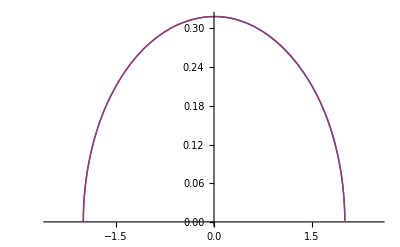

```mathematica
Plot[{AA[x],AAn[x]},{x,-2.5,2.5}]
```

## FreeTimes Examples

We need a  measure supported on the positive real line.  Here we shift the semi circle

```mathematica
VS[x_]:=(x-3)^2;
vfS=SingFun[Fun[VS',VS//EquilibriumMeasureSupport//Line],{0,0}];
emS=(-1/(2 π) vfS//HilbertInverse);
```

```mathematica
SxS=emS~FreeTimes~emS;
```

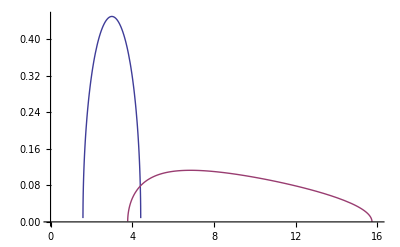

```mathematica
Plot[{emS[x],SxS[x]},{x,0,16}]
```

```mathematica
SxMP=emS~FreeTimes~MP;
```

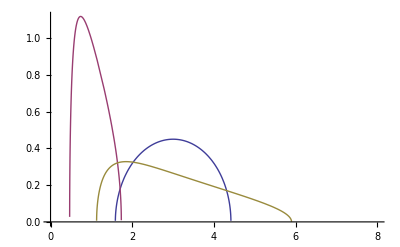

```mathematica
Plot[{emS[x],MP[x],SxMP[x]},{x,0,8}]
```

### Histograms

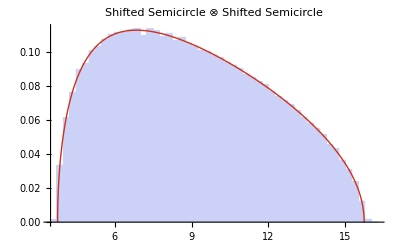

```mathematica
n=300;
HistogramPlot[(
A2=RandomSymmetric[n]+3 IdentityMatrix[n];
A=MatrixPower[A2,1/2];
B=RandomSymmetric[n]+3 IdentityMatrix[n];
A.B.A),SxS,PlotLabel->"Shifted Semicircle ⊗ Shifted Semicircle"]
```

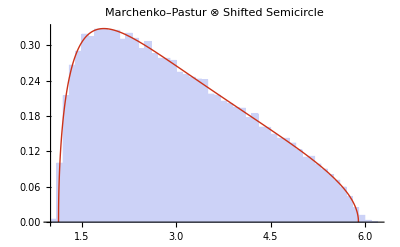

```mathematica
m=100;n=10 m;
HistogramPlot[(
A2=RandomSymmetric[m]+3 IdentityMatrix[m];
A=MatrixPower[A2,1/2];
B=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
A.B.Transpose[B].A),SxMP,PlotLabel->"Marchenko–Pastur ⊗ Shifted Semicircle"]
```

## FreeCompress Examples

```mathematica
comA2=FreeCompress[emA,.2];
comA4=FreeCompress[emA,.4];
comA8=FreeCompress[emA,.8];
```

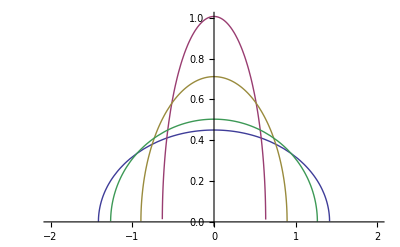

```mathematica
Plot[{emA[x],comA2[x],comA4[x],comA8[x]},{x,-2,2}]
```

```mathematica
comB2=FreeCompress[emB,.2];
comB4=FreeCompress[emB,.4];
comB8=FreeCompress[emB,.8];
```

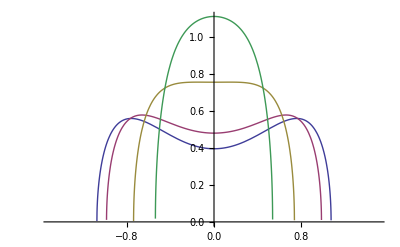

```mathematica
Plot[{emB[x],comB8[x],comB4[x],comB2[x]},{x,-1.5,1.5}]
```

```mathematica
comC2=FreeCompress[emC,.2];
comC4=FreeCompress[emC,.4];
comC8=FreeCompress[emC,.8];
```

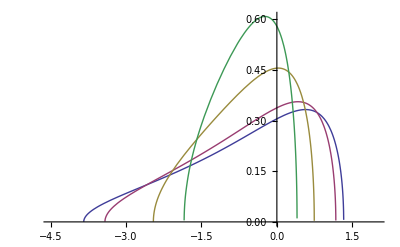

```mathematica
Plot[{emC[x],comC8[x],comC4[x],comC2[x]},{x,-4.5,2}]
```

```mathematica
MP2=FreeCompress[MP,.2];
MP4=FreeCompress[MP,.4];
MP8=FreeCompress[MP,.8];
```

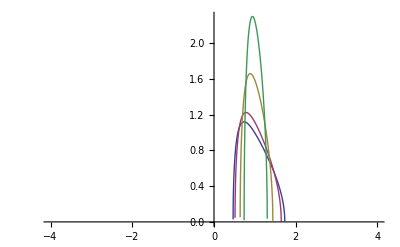

```mathematica
Plot[{MP[x],MP8[x],MP4[x],MP2[x]},{x,-4.,4.}]
```

Now for the Gaussian example.

```mathematica
comG2=FreeCompress[G,.2];
comG4=FreeCompress[G,.4];
comG8=FreeCompress[G,.8];
```

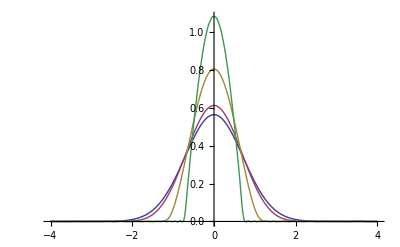

```mathematica
Plot[{G[x]//Re,comG8[x]//Re,comG4[x]//Re,comG2[x]//Re}//Evaluate,{x,-4,4}]
```

### Histograms

We can compare with histograms

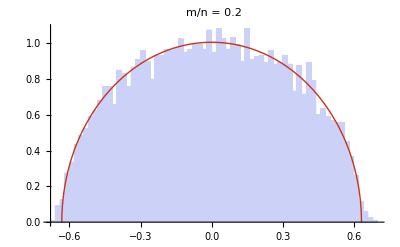

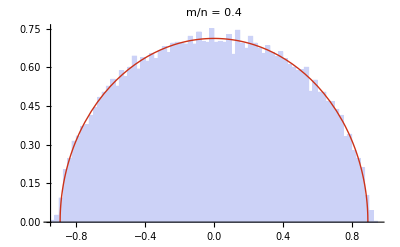

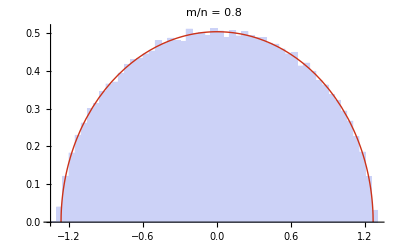

```mathematica
n=300;
m=2/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧),comA2,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;

m=4/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧),comA4,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;

n=300;
m=8/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧),comA8,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;
```

We can compare with histograms

```mathematica
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
A.Transpose[A]
```

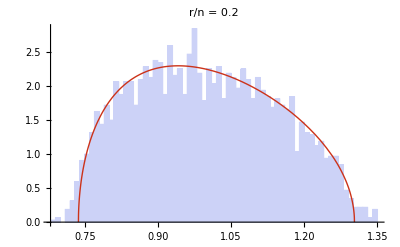

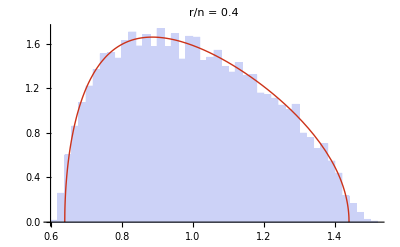

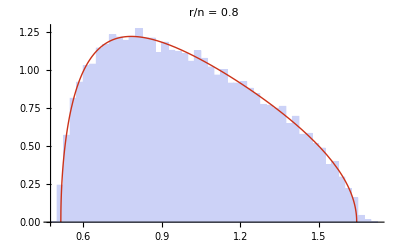

```mathematica
m=80;n=10 m; r=2/10 m;

HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
Q=RandomOrthogonal[m];
(Q.A.Transpose[A].Transpose[Q])⟦;;r,;;r⟧),MP2,PlotLabel->"r/n = "<>ToString[r/m//N]]//Print;

r=4/10 m;

HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
Q=RandomOrthogonal[m];
(Q.A.Transpose[A].Transpose[Q])⟦;;r,;;r⟧),MP4,PlotLabel->"r/n = "<>ToString[r/m//N]]//Print;

r=8/10 m;

HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
Q=RandomOrthogonal[m];
(Q.A.Transpose[A].Transpose[Q])⟦;;r,;;r⟧),MP8,PlotLabel->"r/n = "<>ToString[r/m//N]]//Print;
```